```mathematica
SetDirectory[NotebookDirectory[]];
Get["../lib/lib2.m"];
Get["../lib/util.m"];
```

```mathematica
data = Import["../../runs/Trials/N5K6/36559470.dat"];
```

```mathematica
changeNK[5, 6];
```

```mathematica
TrX1sq[line_] := Module[{x1}, (
x1 = line[[2;; 1+(($N)^2-1)]];
{First@line, 1/2 x1.x1}
)];
TrX1X2[line_] := Module[{x1, x2}, (
x1 = line[[2;; 1+(($N)^2-1)]];
x2 = line[[2+(($N)^2-1);; 1+2(($N)^2-1)]];
{First@line, 1/2 x1.x2}
)];
```

```mathematica
trX1sq = TrX1sq/@data;
trX1X2 = TrX1X2/@data;
```

```mathematica
Mean[trX1X2[[All, 2]]]
```

-0.00466967

```mathematica
Mean[trX1sq[[All, 2]]]
```

0.354075

```mathematica
StandardDeviation[trX1X2[[All, 2]]]
```

0.0866544

```mathematica
StandardDeviation[trX1sq[[All, 2]]]
```

0.126876

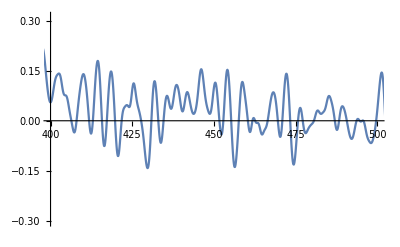

```mathematica
ListPlot[trX1X2, PlotRange->{{400, 500}, Automatic}, Joined->True]
```